# Mathematica

## May 2: Introduction to various functions

Plus and Times function: Even little children know what it does
Subtract function:

```mathematica
Subtract[a,b]
```

a-b

Lists:

```mathematica
list={1,2,3,4,5};
list = List[1,2,3,4,5]
```

{1,2,3,4,5}

Range Function-> Range[Start, Stop, Step] (Stop is EXCLUSIVE)
Also, Range[Something] = {1, 2, 3... Something]

```mathematica
Range[5]
Range[1,2,0.1]
```

{1,2,3,4,5}

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

List of ones or List of zeroes hacks:

```mathematica
Range[1,10]^0
Range[1,10]*0
```

{1,1,1,1,1,1,1,1,1,1}

{0,0,0,0,0,0,0,0,0,0}

But proper legal way:

```mathematica
Table[1,10]
```

{1,1,1,1,1,1,1,1,1,1}

Accessing particular element of list: Array [[]] (double square bracket)

```mathematica
list=  Range[10];
list[[5]]
```

5

## May 5: Function definitions, Mapping functions

Hold function-> doesn’t evaluate function

```mathematica
Hold[Plus[1, 1]]
```

Hold[1+1]

FullForm -> Prints the entire expression in full form. We need to use FullForm[Hold[Something]] to prevent mathematica from evaluate the damn thing.

```mathematica
FullForm[Hold[1 + 1 / 2 * 15 ^2]]
```

Hold[Plus[1,Times[Times[1,Power[2,-1]],Power[15,2]]]]

Postfix ->”//” -> applies function
Prefix -> “@ ()” -> applies function

```mathematica
1 + 2 // Hold // FullForm
FullForm@(Hold@(1 + 2))
```

Hold[Plus[1,2]]

Hold[Plus[1,2]]

Applying function to each element of array:
function / @ array

```mathematica
f /@({1,2,3})
```

{f[1],f[2],f[3]}

Defining our own function

```mathematica
f[x_, y_] = x * y (*Evaluates the function itself, which is why we see output of function itself*)
f[x_, y_] := x * y (* Doesn't evaluate the function right now, we don't see output of function itself*)
f[1,2]
```

x y

2

% -> apply something to output of previous input
%% -> two steps previous, etc.
Personally, NEVER USE THIS.

```mathematica
list = {1,2,3}
```

{1,2,3}

```mathematica
Reverse[%]
```

{4,3,2,1}

## May 5: Strings and Arrays

Dropping first n elements

```mathematica
StringDrop["string", 3]
```

ing

```mathematica
StringReplace["string", "t" -> "F"]
```

sFring

Import Text

```mathematica
(*Import["path"]
Export["path", data]*)
```

List -> Vector
Array -> Matrix -> just a nested list
Display using //MatrixForm
Visualizing lists: ListPlot function

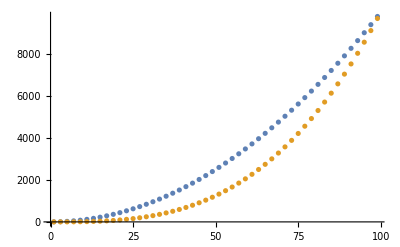

```mathematica
table1 = Table[{i, i^2}, {i, 1, 100, 2}];
table2  =  Table[{i, (i^3)/100}, {i, 1, 100, 2}];
ListPlot[{table1, table2}]
```

Things to do while plotting stuff:
- AxesLabel
- PlotLabel
- PlotLegends
- FrameLable
- Frame

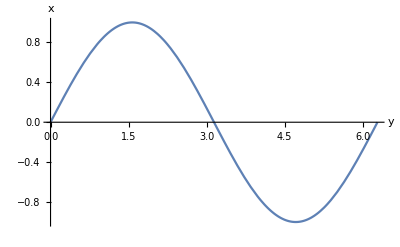

```mathematica
Plot[Sin[x], {x, 0, 2 * Pi}, AxesLabel-> {"y","x"}]
```

Log plots are nice!

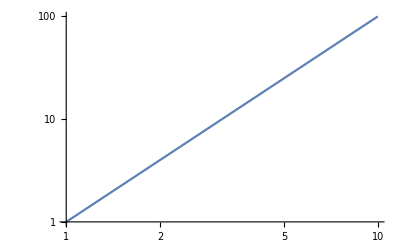

```mathematica
LogLogPlot[i^2,{i, 1, 10}]
```

Bottom line is, there are parametric plots, etc., many different kinds of plots
VectorPlot:

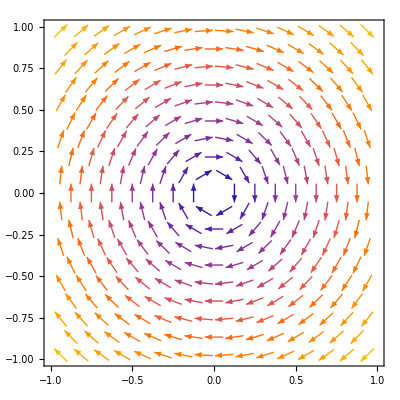

```mathematica
VectorPlot[{y, -x}, {x, -1, 1}, {y, -1, 1}]
```

## May 9th

Whole numbers
“1.” is a decimal

```mathematica
1./2
```

0.5

```mathematica
1/2
```

1/2

Function that computes numerical value of anything

```mathematica
N[1/2]
```

0.5

Precision: With what precision does Mathematica deal with these numbers
- Whole numbers: infinite precision
- Decimal: MachinePrecision, it treats decimals with 16 digit precision
N function -> Machine Precision

```mathematica
1/2 //Precision
```

∞

```mathematica
1.0//Precision
```

MachinePrecision

```mathematica
$MachinePrecision
```

15.9546

```mathematica
Pi//Precision
N[Pi]//Precision
```

∞

MachinePrecision

N [Pi, 100], prints something with 100 digit precision

```mathematica
N[Pi, 100.2]//Precision
```

100.2

SetPrecision -> Rounds off outputs, outputs looks cleaner

```mathematica
a = SetPrecision[Pi, 3]
Precision[a]
```

3.14

3.

Curve Fitting

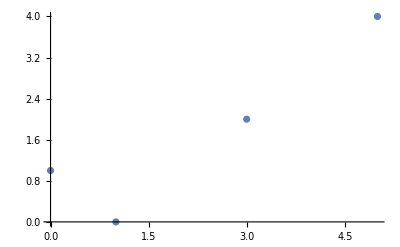

```mathematica
data = {{0,1}, {1,0},{3,2}, {5,4}};
ListPlot[data]
```

```mathematica
linearFit=  Fit[data, {1,x},x ]
```

0.186441+0.694915 x

```mathematica
quadraticFit = Fit[data, {1, x, x^2}, x]
```

0.678392-0.266332 x+0.190955 x^2

```mathematica
cubicFit = Fit[data ,{1,x, x^2, x^3}, x]
```

1.-2.06667 x+1.2 x^2-0.133333 x^3

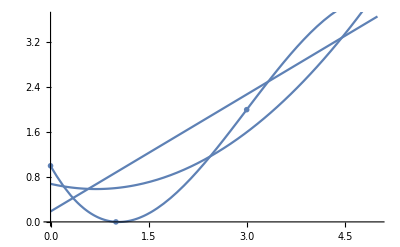

```mathematica
Show[Plot[linearFit, {x ,0, 5}], ListPlot[data , PlotMarkers->{Red, Medium}], Plot[quadraticFit, {x, 0, 5}], Plot[cubicFit, {x, 0, 5}]]
```

Extracting x values:
Sum of squares of differences between y-coordinates -> residual

```mathematica
xdata = data[[All, 1]]
```

{0,1,3,5}

```mathematica
ydata = data[[All, 2]]
```

{1,0,2,4}

```mathematica
Clear[a]
residual = ydata - a - b * xdata
```

{1-a,-a-b,2-a-3 b,4-a-5 b}

```mathematica
errSq = Norm[residual]^2;
Minimize[errSq, {a, b}]//N
```

{1.62712,{a→0.186441,b→0.694915}}

```mathematica
ReplaceAll[errSq, {a->0.1864406779661017,b->0.6949152542372882}]
```

1.62712

For cubicFit, error is 0

```mathematica
41.0/59
```

0.694915

Interpolation ensures that the function that we’re putting in has same values as the dataset at given points

```mathematica
f = Interpolation[data, InterpolationOrder->2];
```

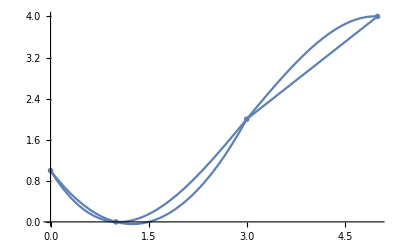

```mathematica
Show[ListPlot[data, PlotMarkers->{Red, 10}], Plot[f[x], {x, 0, 5}], Plot[cubicFit, {x, 0, 5}]]
```

{0.813559,-0.881356,-0.271186,0.338983}

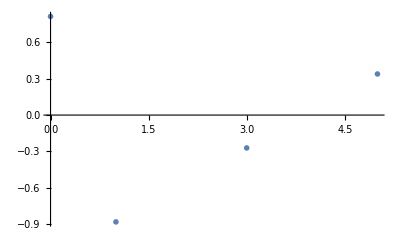

```mathematica
evaluatedResiduals = ReplaceAll[residual, {a-> 0.1864406779661017, b->0.6949152542372882}]
ListPlot[Transpose[{ {0, 1, 3, 5},evaluatedResiduals}], PlotMarkers->{Red, Large}]
```

FindFit function fits to whatever model we have in mind

```mathematica
Clear[x, a, b, c]
data = {{0,1}, {1,0},{3,2}, {5,4}};
FindFit[data, a +b * x + c * x ^2, {a, b, c}, x]
```

{a→0.678392,b→-0.266332,c→0.190955}

Using Linear Model Fit it smart and nice

```mathematica
Clear[x]
linearModel = LinearModelFit[data, {1, x, x^2}, x];
linearModel//Normal
```

0.678392-0.266332 x+0.190955 x^2

```mathematica
linearModel["Properties"];
```

```mathematica
linearModel["FitResiduals"]
```

{0.321608,-0.603015,0.40201,-0.120603}

## May 19th

Include Constant Basis

```mathematica
IncludeConstantBasis->False
```

Interpolation Polynomial

```mathematica
data = {{0,1}, {1,0},{3,2}, {5,4}};
InterpolatingPolynomial[data, x]//Expand//N
```

1.-2.06667 x+1.2 x^2-0.133333 x^3

## Statistics Stuff

Mean

```mathematica
xdata = data[[All, 1]];
ydata = data[[All, 2]];
```

```mathematica
Sum[ydata[[i]], {i, 1, Length[ydata]}]/Length[ydata]//N
```

1.75

```mathematica
sortedData = Sort[ydata];
(sortedData[[2]] + sortedData[[3]])/2
```

3/2

```mathematica
Sqrt[Sum[ydata[[i]]^2, {i, 1, Length[ydata]}]/Length[ydata]]
```

(√21)/2

```mathematica
variance = ((ydata - Mean[ydata]).(ydata - Mean[ydata]) )/(Length[ydata] - 1)
Variance[ydata]
```

35/12

35/12

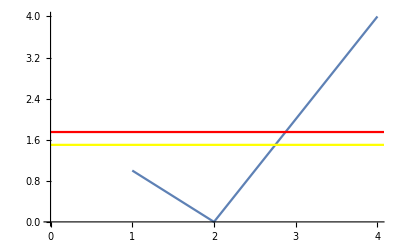

```mathematica
Show[ListPlot[ydata, Joined->True], Plot[Mean[ydata], {x, xdata[[1]], xdata[[4]]}, PlotStyle->Red], Plot[Median[ydata], {x, xdata[[1]], xdata[[4]]}, PlotStyle->Yellow]]
```

Gaussian Distribution

```mathematica
PDF[NormalDistribution[], x]
```

(ⅇ^(-x^2/2))/(√(2 π))

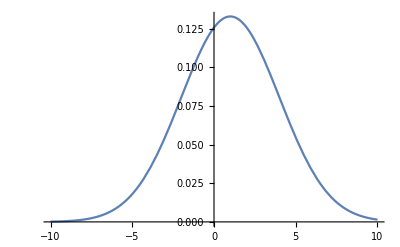

```mathematica
Plot[PDF[NormalDistribution[1, 3], x], {x, -10, 10}]
```

Piecewise[{{(ⅇ^-λ λ^n)/(n!), n≥0}, {0, True}}]

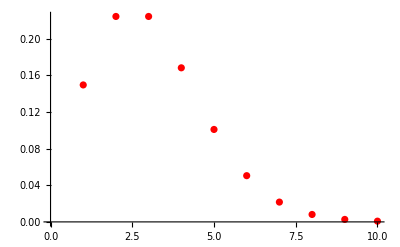

```mathematica
PDF[PoissonDistribution[λ], n]
ListPlot[Table[{x, PDF[PoissonDistribution[3],x]},{x, 1, 10} ], PlotStyle->{Red}]
```

```mathematica
f[x_]= CDF[NormalDistribution[μ, σ], x]
PDF[NormalDistribution[μ, σ], x]
f'[x]
```

1/2 Erfc[(-x+μ)/(√2 σ)]

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

(ⅇ^(-(-x+μ)^2/(2 σ^2)))/(√(2 π) σ)

Random sampling

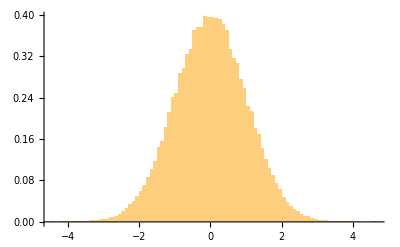

```mathematica
data = RandomVariate[NormalDistribution[], 100000];
Histogram[data, 80, "PDF"]
```

Random Number Generation
- RandomReal
- RandomInteger
-

```mathematica
RandomReal[{0, 5}, {2,3}]//MatrixForm
```

(3.55638 | 4.15562 | 3.0022
3.4098 | 3.98254 | 0.314859)

```mathematica
RandomInteger[{5, 100}, {2,2}]//MatrixForm
```

(28 | 75
46 | 72)

```mathematica
RandomComplex[{1 + I, 2 + 2*I}, {3,2,3}]//MatrixForm
```

((1.03937+1.4448 ⅈ
1.44625+1.52948 ⅈ
1.50594+1.92775 ⅈ) | (1.93362+1.77331 ⅈ
1.23159+1.19644 ⅈ
1.29524+1.01592 ⅈ)
(1.25871+1.21174 ⅈ
1.84527+1.77788 ⅈ
1.7785+1.02949 ⅈ) | (1.88315+1.53721 ⅈ
1.77442+1.37902 ⅈ
1.48515+1.42742 ⅈ)
(1.06276+1.05404 ⅈ
1.85728+1.15774 ⅈ
1.36199+1.2433 ⅈ) | (1.70098+1.96738 ⅈ
1.02702+1.93568 ⅈ
1.97101+1.19088 ⅈ))

Random Seed fixing

```mathematica
SeedRandom["TestNormalDistribution"]
```

RandomGeneratorState[…]

RandomGeneratorState[…]

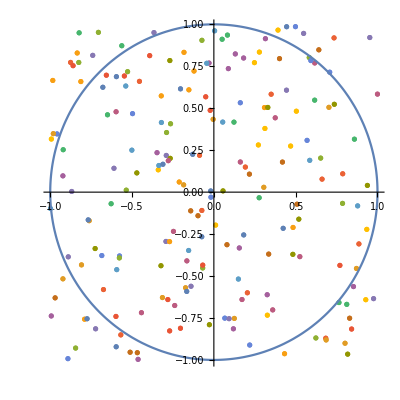

3.14112

-0.000472654

```mathematica
n = 100000;
SeedRandom[0]
table = Table[{RandomReal[{-1, 1}, 2]}, {x, 1, n}];
insideQ[point_] = If[Norm[point] <= 1, True, False];
Show[ListPlot[RandomSample[table, 200]] , ParametricPlot[{Sin[t], Cos[t]}, {t, 0, 2*Pi}], AspectRatio->1
]
monteCarloPi = Count[Map[insideQ, table], True]*4/n//N
monteCarloPi - Pi
```

```mathematica
?RandomSample
```